# λ Loop Example

Anil Radhakrishnan, John F. Lindner, Scott T. Miller, Sudeshna Sinha, William L. Ditto, 
"Growing Neural Networks: Dynamic Evolution through Gradient Descent" 
for Figures 6 & 7.

## Preamble

```mathematica
$Version
```

14.1.0 for Mac OS X ARM (64-bit) (July 16, 2024)

```mathematica
Clear["Global`*"]
```

## Prep

### Parameters

```mathematica
(* randomSeed=236; SeedRandom[randomSeed]; *)
```

```mathematica
nSkip=4;
nTrainData=32; (* number of training pairs *)
nTestData=nTrainData/nSkip;(* number of test pairs *)
```

```mathematica
{10^3,10^3.25,10^3.5,10^3.75,10^4,10^4.25,10^4.5}
```

{1000,1778.28,3162.28,5623.41,10000,17782.8,31622.8}

```mathematica
nEpochs=10^4.25; (* number of training rounds *)
nTrials=200;(* number of trials *)
η=0.001;(* learning rate *)
```

```mathematica
nH=9; (* maximum number of neurons in the hidden layer *)
Ν∞=5; (* desired final network size *)
δn=1;(* add or delete step size *)
```

### Gradual Step Function

```mathematica
θ[n_]:=Piecewise[{{0, n<0}, {Sin[(π n)/(2δn)]^2, 0<=n<=δn}, {1, δn<n}}]
```

### Static Activation Function

```mathematica
σ[z_]:=Tanh[z]
```

### Target Function Bessel

```mathematica
fRaw[x_]:=BesselJ[0,x]
```

```mathematica
xMin=0.1;
xMax=0.2;
fMin = NMinimize[{fRaw[x], xMin< x < xMax}, x][[1]];
fMax = NMaximize[{fRaw[x], xMin < x < xMax}, x][[1]]; 
f[x_]=Rescale[fRaw[Rescale[x,{-1, 1},{xMin, xMax}]],{fMin, fMax},{-1, 1}];
```

### Network

```mathematica
bVec[2]=Array[b[2],{nH}];
bVec[3]=Array[b[3],{1}];
```

```mathematica
wMat[2]=Array[w[2],{nH,2}];
wMat[3]=Array[w[3],{1,nH}];
```

```mathematica
wb={Ν,Table[{wMat[n],bVec[n]},{n,2,3}]}//Flatten;
```

### Losses

```mathematica
yHat[x_]=b[3][1]+∑_(m=1)^nH w[3][1,m]θ[Ν-m+1]σ[b[2][m]+Ν w[2][m,1]+x w[2][m,2]];
L0[{x_,y_}]=(y-yHat[x])^2;(* square error *)
```

```mathematica
xyTrainData=Table[{x[n],y[n]},{n,nTrainData}];
xyTestData=Table[{x[n],y[n]},{n,nTestData}];
```

```mathematica
LTrain=Mean[L0/@xyTrainData]+λ(Ν-Ν∞)^2;(* for batch gradient descent *)
LTest=Mean[L0/@xyTestData]+λ(Ν-Ν∞)^2; (* needs λ *)
```

### Compiles

```mathematica
λwbxyTrain={λ,wb,xyTrainData}//Flatten; (* weights & bias+interleaved x & y *)
λwbxyTest={λ,wb,xyTestData}//Flatten;
```

```mathematica
LTrainC=Compile[{#,_Real}&/@λwbxyTrain//Evaluate,LTrain//Evaluate];
LTestC=Compile[{#,_Real}&/@λwbxyTest//Evaluate,LTest//Evaluate];
```

```mathematica
dLTraindWb=D[LTrain,{wb}];(* Jacobian matrix *)
dLTestdWb=D[LTest,{wb}];
```

```mathematica
dLTraindWbC=Compile[{#,_Real}&/@λwbxyTrain//Evaluate,dLTraindWb//Evaluate];
dLTestdWbC=Compile[{#,_Real}&/@λwbxyTest//Evaluate,dLTestdWb//Evaluate];
```

## Loop

```mathematica
loop[λ_]:=Module[{LFinalGrowing,LFinalGrown},

trainingPairs={#,f[#]}&/@RandomReal[{-1,1},nTrainData];
testingPairs={#,f[#]}&/@RandomReal[{-1,1},nTestData];

computeFinalTestLoss[ΝStart_]:=Module[{wbSample,wbxyTrainData,wbxyTestData,e},
wbSample={ΝStart}~Join~RandomReal[{-1,1},Length@wb-1];

For[ e=1,e<=nEpochs,e++, (* batch gradient descent *)
wbxyTrainData={λ,wbSample,trainingPairs}//Flatten;
wbSample-=η dLTraindWbC@@wbxyTrainData ;(* update Wb *)
trainingPairs=RandomSample@trainingPairs; (* shuffle *)
];

wbxyTestData={λ,wbSample,testingPairs}//Flatten;
{LTestC@@wbxyTestData,λ(wbSample[[1]]-Ν∞)^2}
];

LFinalGrowing=ParallelTable[computeFinalTestLoss[0],{n,nTrials}];
LFinalGrown=ParallelTable[computeFinalTestLoss[Ν∞],{n,nTrials}];

{λ,Mean@LFinalGrowing,Mean@LFinalGrown}
]
```

```mathematica
test=loop[0.266]//AbsoluteTiming
```

{51.0869,{0.266,{0.0148718,2.11916×10^-7},{0.0204331,1.82557×10^-7}}}

## Experiment

```mathematica
Δlogλ=0.01;
```

```mathematica
experimentTime=(test[[1]] 4/Δlogλ)/3600 hours
```

5.67632 hours

```mathematica
AbsoluteTiming[
λL0L5s=Table[loop[10^logλ],{logλ,-2,2,Δlogλ}];
][[1]]/60^2 hours
```

5.53577 hours

```mathematica
λRs={#[[1]],(#[[2,1]])/(#[[3,1]])}&/@λL0L5s;
```

```mathematica
λLs={#[[1]],#[[2,1]]}&/@λL0L5s;
```

```mathematica
λL0s={#[[1]],#[[2,1]]-#[[2,2]]}&/@λL0L5s;
```

```mathematica
λδLs={#[[1]],#[[2,2]]}&/@λL0L5s;
```

```mathematica
average[data_,rad_]:=Transpose[{data[[Round[(rad+1)/2]-1;;Length@data-Round[(rad-1)/2]-1,1]],MovingAverage[data[[All,2]],rad]}]
```

```mathematica
RRawPlot=ListLogLogPlot[λRs
,PlotRange->{{0.0085,120},{0.1,100}}
,Joined->False
,Mesh->All
,AspectRatio->1
,Frame->True
,FrameLabel->{"size coupling λ",Rotate["L_growing^final/L_grown^final",-90°]}
,FrameTicksStyle->18
,FrameStyle->24
,LabelStyle->{FontFamily->"CMU Serif",Black}
,PlotStyle->Gray
,ImageSize->500
,GridLines->{None,{1}}
,GridLinesStyle->Directive[Red,Thick, Dashed]
];
```

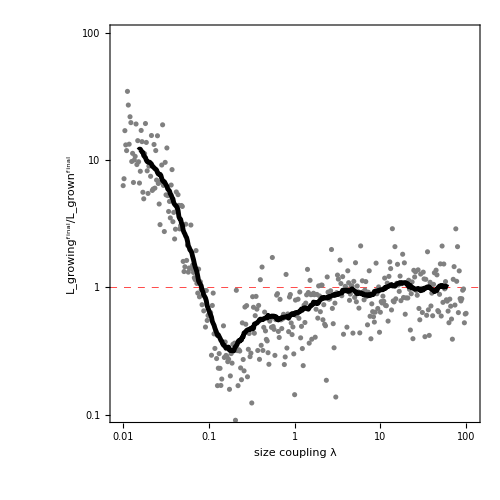

```mathematica
Show[RRawPlot,
ListLogLogPlot[average[λRs,40],Joined->True,PlotStyle->Directive[Thickness[0.007],Black]]
]
```

```mathematica
LGrowRawPlot=ListLogLogPlot[λLs
,PlotRange->{{0.0085,120},All}
,Joined->False
,Mesh->All
,AspectRatio->1
,Frame->True
,FrameLabel->{"size coupling λ",Rotate["L_growing^final",-90°]}
,FrameTicksStyle->18
,FrameStyle->24
,LabelStyle->{FontFamily->"CMU Serif",Black}
,PlotStyle->Gray
,ImageSize->500
];
```

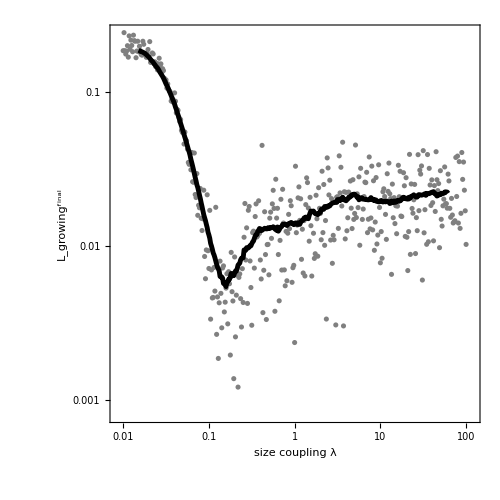

```mathematica
Show[LGrowRawPlot,
ListLogLogPlot[average[λLs,40],Joined->True,PlotStyle->Directive[Thickness[0.007],Black]]
]
```

```mathematica
λL0GrowPlot=ListLogLogPlot[λL0s
,PlotRange->{{0.0085,120},{0.005,1}}
,Joined->False
,Mesh->All
,AspectRatio->1
,Frame->True
,FrameLabel->{"size coupling λ",Rotate["L_0_growing^final",-90°]}
,FrameTicksStyle->18
,FrameStyle->24
,LabelStyle->{FontFamily->"CMU Serif",Black}
,PlotStyle->Gray
,ImageSize->500
];
```

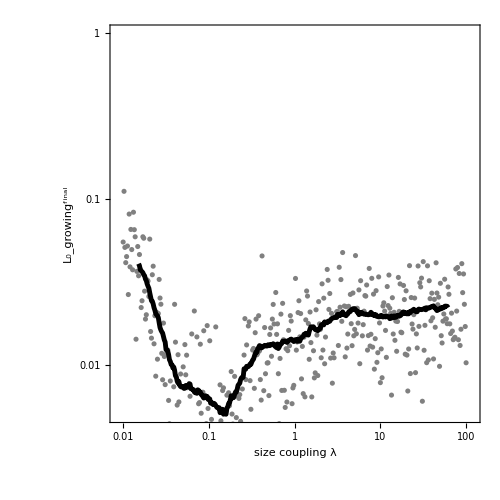

```mathematica
Show[λL0GrowPlot,
ListLogLogPlot[average[λL0s,40],Joined->True,PlotStyle->Directive[Thickness[0.007],Black]]
]
```

```mathematica
λδLGrowPlot=ListLogLogPlot[λδLs
,PlotRange->{{0.0085,120},All}
,Joined->False
,Mesh->All
,AspectRatio->1
,Frame->True
,FrameLabel->{"size coupling λ",Rotate["δL_growing^final",-90°]}
,FrameTicksStyle->18
,FrameStyle->24
,LabelStyle->{FontFamily->"CMU Serif",Black}
,PlotStyle->Gray
,ImageSize->500
];
```

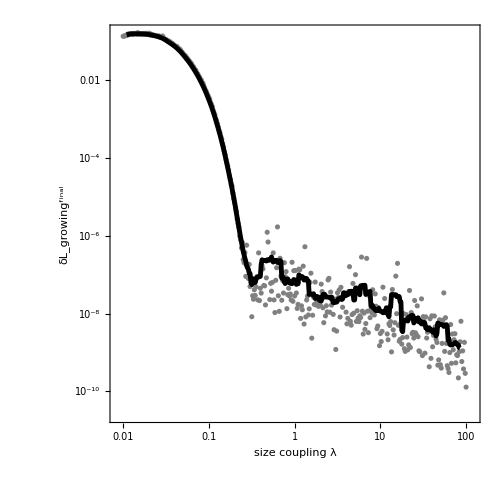

```mathematica
Show[λδLGrowPlot,
ListLogLogPlot[average[λδLs,12],Joined->True,PlotStyle->Directive[Thickness[0.007],Black]]
]
```

## Data Storage

```mathematica
λL0L5sStored=;
```